# Segmentation using Mathematical Morphology

There are multiple ways to do segmentation, mathematical morphology is a geometric approach for extracting image components that are useful in the representation and description of region shape. In this exploration, we illustrate several basic concepts in mathematical morphology, such as erosion, dilation, opening, and closing. And we will examine how to apply those simple operators to perform segmentation on medical images.

## Introduction of Segmentation

Our task is separating object from background in a grayscale picture. Here is an example:

-Graphics-⟶-Graphics-

#### Helper functions

```mathematica
SetDirectory[ToFileName[Extract["FileName"/.NotebookInformation[EvaluationNotebook[]],{1},FrontEnd`FileName]]];
PNGtoGray[filename_]:=Reverse[Map[Map[First,#]&,Import[filename,"Data"]]];
GIFtoGray[filename_]:=255-Reverse[Map[Map[First,#]&,Import[filename,"Data"]]];
showGrayImage[img_]:=Graphics[Raster[img/Max[img]],Frame->False];
showBinaryImage[img_]:=Graphics[Raster[img],Frame->False];
showBinaryOverlay[img_,mask_]:=Graphics[Raster[MapThread[MapThread[If[#2==1,{1,0,0},{#1,#1,#1}]&,{#1,#2}]&,
{img,mask}]],Frame->False];
showGrayOverlay[img_,mask_]:=Graphics[{Raster[img/Max[img]],Raster[Map[Map[{#,0,0,If[#==1,.5,0]}&,#]&,mask]]},Frame->False];
toBinary[x_, threshold_]:= If[x > threshold, 1, 0]
getBinarizedImage[img_, threshold_]:= (toBinary[#, threshold] &/@ ((N @ img⟦#⟧ / 255)) &/@ (Range[Length[img]]))
```

```mathematica
kernelFromStructure[structure_] := Block[
	{size = 2 Max @ Abs @ MinMax @ structure + 1},
	ReplacePart[Table[0, size, size], Thread[Append[structure, {0, 0}] + (size + 1)/2 -> 1]]
]
```

```mathematica
kernelFromStructure[structure_] := Block[
	{size = 2 Max @ Abs @ MinMax @ structure + 1},
	ReplacePart[Table[0, size, size], Thread[Append[structure, {0, 0}] + (size + 1)/2 -> 1]]
]

erode[imageData_, structure_, n_] := Nest[erode[#, structure] &, imageData, n]

erode[imageData_, structure_] := Block[
	{
		kernel = (* Transpose @ *) kernelFromStructure[structure],
		paddedData, neighborhoods, validNeighbors, newPixels
	},
	paddedData = 1 - ArrayPad[imageData, (Length @ kernel - 1)/2, 1];
	neighborhoods = Partition[paddedData, Table[Length @ kernel, 2], 1];
	validNeighbors = Map[# * kernel &, neighborhoods, {2}];
	newPixels = 1 - Map[Max, validNeighbors, {2}];
	newPixels
]

dilate[imageData_, structure_, n_]:= Nest[dilate[#, structure] &, imageData, n]

dilate[imageData_,structure_]:= 1 - erode[1 - imageData, structure]

open[imageData_, structure_, r_]:= dilate[erode[imageData, structure, r], structure, r]
close[imageData_, structure_, r_]:= erode[dilate[imageData, structure, r], structure, r]
```

## Connected Components

Definition: A maximum set of pixels (voxels) in the object or background, such that any two pixels (voxels) in the set are connected by a path of connected pixels (voxels).

### Connectivity (2D)

Two pixels are connected if their squares share:

A common edge

4-connectivity

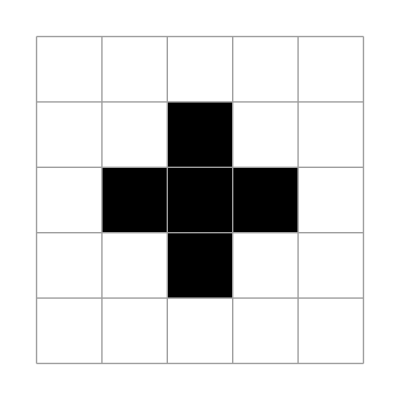

```mathematica
ArrayPlot[{{0,0,0,0,0},{0,0,1,0,0},{0,1,1,1,0},{0,0,1,0,0},{0,0,0,0,0}},Mesh->True]
```

A common vertex

8-connectivity

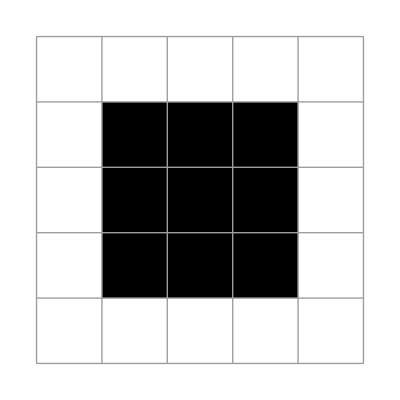

```mathematica
ArrayPlot[{{0,0,0,0,0},{0,1,1,1,0},{0,1,1,1,0},{0,1,1,1,0},{0,0,0,0,0}},Mesh->True]
```

Therefore, based one two types of connectivity, we can have two kinds of operating structure elements:

```mathematica
structCross={{0,1},{0,-1},{1,0},{-1,0}};
structSquare={{-1,-1},{-1,0},{-1,1},{0,1},{1,1},{1,0},{1,-1},{0,-1}};
```

### Finding Connected Components

#### The “flooding” algorithm

Start from a seed pixel / voxel, expand the connected component.

Either do depth-first or breadth-first search (a LIFO stack or FIFO queue)

1. Initialize
	1. Create a result set S that contains only P.
	2. Create a visited flag at each pixel, and set it to be false except for P.
	3. Initialize a queue (or stack) Q that contains only P.
2. Repeat until Q is empty:
	1. Pop a pixel x from Q.
	2. For each unvisited object pixel y connected to x, add y to S, set its flag to be visited, and push y to Q.
3. Output S.

```mathematica
flood[imageData_, givenPixel_, connectivityType_]:= Module[
	{x, y, w, h, struct, center, queue, neighbors, newQueue, newPixels},	
	struct = Switch[connectivityType, 0, structSquare, 1, structCross];	
	{w, h} = Dimensions[imageData];
	newPixels = Table[0, w, h];		
	queue = {givenPixel};
	newPixels⟦givenPixel⟦1⟧, givenPixel⟦2⟧⟧ = 1;	
	While[queue ≠ {},
		center = First @ queue;
		newQueue = Rest[queue];	
		queue = newQueue;		
		neighbors = (center + #) &/@ struct;			
		Scan[If[1 ≤ #⟦1⟧ ≤ w && 1 ≤ #⟦2⟧ ≤ h && imageData⟦#⟦1⟧, #⟦2⟧⟧ == 1 
			&& newPixels⟦#⟦1⟧, #⟦2⟧⟧ == 0,
			AppendTo[queue, {#⟦1⟧, #⟦2⟧}];
			newPixels⟦#⟦1⟧, #⟦2⟧⟧ = 1] &, neighbors];
	];
	newPixels		
]
```

#### Example

Let’s start from a small dataset - a low resolution CT scan of human foot bone.

```mathematica
boneSmall=PNGtoGray["bone_small.png"];
showGrayImage[boneSmall]
```

-Graphics-

```mathematica
binBoneSmall=getBinarizedImage[boneSmall,.5];
showBinaryImage[binBoneSmall]
```

-Graphics-

```mathematica
showBinaryImageComponent[img_]:=Manipulate[showBinaryOverlay[img,
flood[img,Ceiling[Reverse[pt]],Switch[object,
"8-connected",0,"4-connected",1]]],{{pt,Reverse[Dimensions[img]/2]},{1,1},Reverse[Dimensions[img]],Locator},{object,{"8-connected","4-connected"}}]
```

Loop through each pixel, if it’s not labeled, use it as a seed to find a connected component, then label all pixels (voxels) in the component.

```mathematica
showBinaryImageComponent[binBoneSmall]
```

By 8-connectivity, we have one component, while by 4-connectivity, we have 2 components.

## Mathematical Morphology

Structure element B is symmetric if

x∈ B_y⇔ y∈ B_x

#### Morphology Operators

Morphology operators can perform operations to change shapes

Input: object (A) and structure element (B_x)

Erosion

A⊖B ={x∈ A| B_x⊆A}

Erosion of a binary image with a disk - shaped structuring element :

```mathematica
Erosion[-Graphics-,DiskMatrix[3]]
```

-Graphics-

Dilation

A⊕B ={x∈ A|∪_(x∈A)B_x}

Dilation of a binary image with a disk - shaped structuring element :

```mathematica
Dilation[-Graphics-,DiskMatrix[4]]
```

-Graphics-

#### Duality (for symmetric structure elements)

Erosion:

A⊖B = OverBar[Ā⊕B]

Dilation:

A⊕B = OverBar[Ā⊖B]

Opening: erode, then dilate

A∘B = (A⊖B)⊕B

Closing: dilate, then erode

A·B = (A⊕B)⊖B

Complement of union of all B that can fit in the complement of A

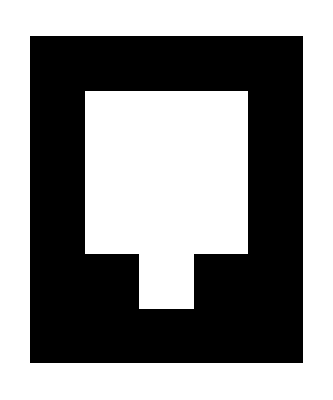

```mathematica
exampleImgData=1-{{1,1,1,1,1},{1,1,0,1,1},{1,0,0,0,1},{1,0,0,0,1},{1,0,0,0,1},{1,1,1,1,1}};
showBinaryImage[exampleImgData]
```

After erosion

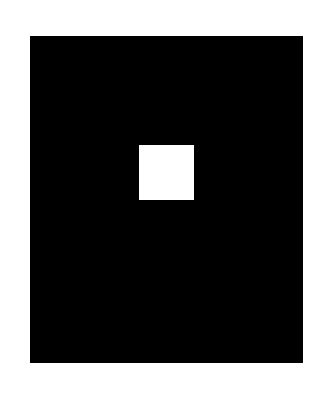

```mathematica
showBinaryImage@erode[exampleImgData,structSquare]
```

After dilation

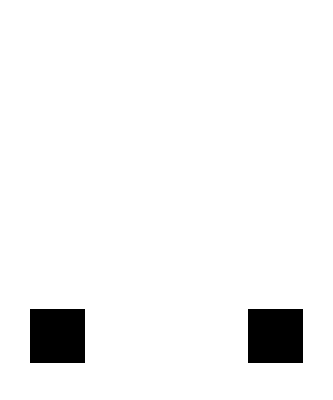

```mathematica
showBinaryImage@dilate[exampleImgData,structSquare]
```

### Example

```mathematica
morphoDynamic[img_]:=Manipulate[
	showBinaryImage[
		Switch[operator,
			"Erode", erode,
			"Dilate", dilate,
			"Open", open,
			"Close", close]
			[img, Switch[element, "Square", structSquare, "Cross", structCross], t]],
			{t, 0, 5, 1},
		{operator, {"Erode", "Dilate", "Open", "Close"}}, {element, {"Square", "Cross"}}]
```

```mathematica
morphoDynamic[binBoneSmall]
```

## Bone Segmentation

#### Code

```mathematica
flood[imageData_, givenPixel_, connectivityType_]:= Module[
	{x, y, w, h, struct, center, queue, neighbors, newQueue, newPixels},	
	struct = Switch[connectivityType, 0, structSquare, 1, structCross];	
	{w, h} = Dimensions[imageData];
	newPixels = Table[0, w, h];		
	queue = {givenPixel};
	newPixels⟦givenPixel⟦1⟧, givenPixel⟦2⟧⟧ = 1;	
	While[queue ≠ {},
		center = First @ queue;
		newQueue = Rest[queue];	
		queue = newQueue;		
		neighbors = (center + #) &/@ struct;			
		Scan[If[1 ≤ #⟦1⟧ ≤ w && 1 ≤ #⟦2⟧ ≤ h && imageData⟦#⟦1⟧, #⟦2⟧⟧ == 1 
			&& newPixels⟦#⟦1⟧, #⟦2⟧⟧ == 0,
			AppendTo[queue, {#⟦1⟧, #⟦2⟧}];
			newPixels⟦#⟦1⟧, #⟦2⟧⟧ = 1] &, neighbors];
	];
	newPixels		
]
```

labelComponents that labels every object pixel of the binary picture by the index of its containing connected component. The function takes two parameters, a binary image img, and a connectivity type conn (see previous algorithm description).  Index the connected components as 1, 2, 3, .... The function returns a grayscale image with the same dimension as img and containing the label at each pixel.

```mathematica
labelComponents[imageData_,connectivityType_] := Module[
	{w, h, partitionedGroup, positionList, rule},	
	{w, h} = Dimensions[imageData];	
	partitionedGroup = Reap[NestWhileList[# - Sow[flood[#, Position[#, 1]⟦1⟧, connectivityType]] &, imageData, # ≠ Table[0, w, h]&]] ⟦2,1⟧;
	positionList = Position[#, 1] &/@ partitionedGroup;		
	rule = Thread /@ MapThread[#1 -> #2 &, {positionList, Range @ Length @ positionList}];
	ReplacePart[Table[0, w, h], Flatten[rule, 1]]
]
```

```mathematica
getLargestComponents[imageData_, k_, connectivityType_]:= Module[
	{w, h, groupedData, intensityVals, numPerGroup, maxSizes, groupSizeWithIntensityValue, 
	maxIntensities, maxIntensityPositions, replaceRules, newPixels},
	
	groupedData = labelComponents[imageData, connectivityType];
	intensityVals = Rest @ Union @ Flatten @ groupedData;
	numPerGroup = Length[Position[groupedData, #]] &/@ intensityVals;

	maxSizes = TakeLargest[k] @ numPerGroup;

	groupSizeWithIntensityValue = Association[MapThread[#1 -> #2 &, {numPerGroup, intensityVals}]];
	maxIntensities = groupSizeWithIntensityValue[#] &/@ maxSizes;

	maxIntensityPositions = Position[groupedData, #] &/@ maxIntensities;
	replaceRules = # -> 1 &/@ maxIntensityPositions;
	
	{w, h} = Dimensions[imageData];
	newPixels = Table[0, w, h];
	ReplacePart[newPixels,replaceRules]
]
```

#### Human foot CT image

Here we will apply this algorithm on a full-resolution CT image of a human foot.

```mathematica
boneLarge=PNGtoGray["bone_large.png"];
showGrayImage[boneLarge]
```

-Graphics-

The first step is to binarize it.

Here by observing, we find:
1. Islands (holes) of the object are holes (islands) of the background
2. Islands (holes) are not as well-connected as the object (background).

```mathematica
boneImgBinary=getBinarizedImage[boneLarge,0.5];
showBinaryImage[boneImgBinary]
```

-Graphics-

Take the largest 2 connected components of the object

```mathematica
bone1=getLargestComponents[boneImgBinary,2,0];
showBinaryImage[bone1]
```

-Graphics-

Then we invert the largest connected component of the background

```mathematica
bone2=close[bone1,structSquare,1];
showBinaryImage[1-bone2]
```

-Graphics-

```mathematica
bone3=1-getLargestComponents[1-bone2,1,0];
showBinaryImage[bone3]
```

-Graphics-

The morphology operators are used to smoothing out object boundary.

```mathematica
bone4=open[bone3,structSquare,3];
showBinaryImage[bone4]
```

-Graphics-

Here we get a segmentation of the bone!

```mathematica
GraphicsRow[{showGrayImage[boneLarge],showGrayOverlay[boneLarge,bone4]}]
```

-Graphics-

## Other Segmentation

If we wrap this process up, we can do segmentation in general to many cases :

#### Mouse brain segmentation

```mathematica
mouseBrain=PNGtoGray["mousebrain.png"];
showGrayImage[mouseBrain]
```

-Graphics-

```mathematica
binMouseBrain=1-getBinarizedImage[mouseBrain,0.97];
showBinaryImage[binMouseBrain]
```

-Graphics-

```mathematica
mb1=getLargestComponents[binMouseBrain,1,0];
showBinaryImage[mb1]
```

-Graphics-

```mathematica
mb2=Floor@close[mb1,structSquare,1];
showBinaryImage[mb2]
```

-Graphics-

```mathematica
mb3=1-getLargestComponents[1-mb2,1,1];
showBinaryImage[mb3]
```

-Graphics-

```mathematica
mb4=open[mb3,structSquare,5];
showBinaryImage[mb4]
```

-Graphics-

```mathematica
GraphicsRow[{showGrayImage[mouseBrain],showGrayOverlay[mouseBrain,mb4]}]
```

-Graphics-

#### Breast Lesion

```mathematica
brLesion=PNGtoGray["breastlesion.png"];
showGrayImage[brLesion]
```

-Graphics-

```mathematica
binBrLesion=getBinarizedImage[brLesion,0.65];
showGrayImage[binBrLesion]
```

-Graphics-

```mathematica
brLargest=getLargestComponents[binBrLesion,1,0];
showBinaryImage[brLargest]
```

-Graphics-

```mathematica
brOpen=open[brLargest,structSquare,4];
showBinaryImage[brOpen]
```

-Graphics-

```mathematica
GraphicsRow[{showGrayImage[brLesion],showGrayOverlay[brLesion,brOpen]}]
```

-Graphics-

Further Explorations

Morphology on Gray Scale Images
	Retinal Vessel Segmentation
	code:  
	paper:

Corneal Ulcer Segmentation
	project page:

Authorship information

Wenzhen Zhu

06/23/2017

zhu_wenzhen@icloud.com